```mathematica
K=10;(*Soil quality upper limit*)
γ=0.6;(*Randomisation between cash and cover*)
p=0.4;(*Probability of making a profit on cover crops*)
p1=0.0;(*Probability of making a profit on cash crops when soil quality is bad*)
p2=0.8;(*Probability of making a profit on cash crops when soil quality is good*)
θ=3;(*threshold soil quality required by the cash crop to make a profit*)
a=1;
b=-1;
cashyield=1;
cashloss=-1;
```

```mathematica
overgamma={};
For[i=1,i≤3,i++,
γ={0.0,0.6,1.0}⟦i⟧;
profitslist={};
maxrealisations=1000;
For[realisation=1,realisation≤maxrealisations,realisation++,
soilquality={0};
profit={0};
runtime=1000;
For[time=1,time≤runtime,time++,
currentsoilquality=Total[soilquality];
If[RandomReal[]≤γ,
(*Cover crops*)
If[currentsoilquality<K,AppendTo[soilquality,a],AppendTo[soilquality,0]];
If[RandomReal[]≤p,AppendTo[profit,cashyield],AppendTo[profit,cashloss]];,
(*Cash crops*)
If[currentsoilquality≤θ,
If[RandomReal[]≤p1,AppendTo[profit,cashyield],AppendTo[profit,cashloss]];,
If[RandomReal[]≤p2,AppendTo[profit,cashyield],AppendTo[profit,cashloss]];];
If[currentsoilquality>0,AppendTo[soilquality,b],AppendTo[soilquality,0]];
]
];
AppendTo[profitslist,Accumulate[profit]]
];
AppendTo[overgamma,profitslist];
]
```

```mathematica
randomisedzeoptsix={overgamma⟦2⟧,Mean[overgamma⟦2⟧]};
cashcrops={overgamma⟦1⟧,Mean[overgamma⟦1⟧]};
covercrops={overgamma⟦3⟧,Mean[overgamma⟦3⟧]};
stochcover=Take[overgamma⟦3⟧,{1,Length[overgamma⟦3⟧],10}];
stochcash=Take[overgamma⟦1⟧,{1,Length[overgamma⟦1⟧],10}];
stochrand=Take[overgamma⟦2⟧,{1,Length[overgamma⟦2⟧],10}];
```

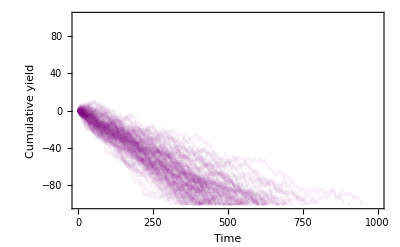

```mathematica
stochcoverpl=ListPlot[stochcover,Joined->True,PlotStyle->Directive[Opacity[0.05],Purple],PlotRange->{All,{-101,101}},Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Time",14,Black],Style["Cumulative yield",14,Black]}]
```

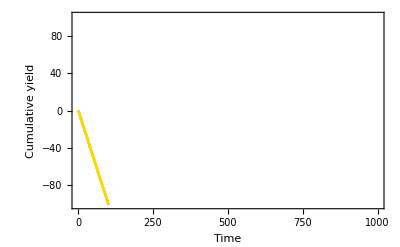

```mathematica
stochcashpl=ListPlot[stochcash,Joined->True,PlotStyle->Directive[Opacity[0.05],gold],PlotRange->{All,{-101,101}},Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Time",14,Black],Style["Cumulative yield",14,Black]}]
```

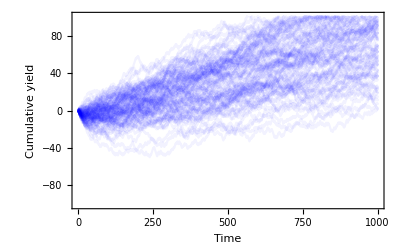

```mathematica
stochrandpl=ListPlot[stochrand,Joined->True,PlotStyle->Directive[Opacity[0.05],Blue],PlotRange->{All,{-101,101}},Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Time",14,Black],Style["Cumulative yield",14,Black]}]
```

```mathematica
gold=RGBColor["#FFD700"];
```

```mathematica
mainpl=ListPlot[{randomisedzeoptsix⟦2⟧,cashcrops⟦2⟧,covercrops⟦2⟧},PlotRange->{All,{-101,101}},Joined->True,PlotStyle->{Blue,gold,Purple},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Time",14,Black],Style["Cumulative yield",14,Black]}];
```

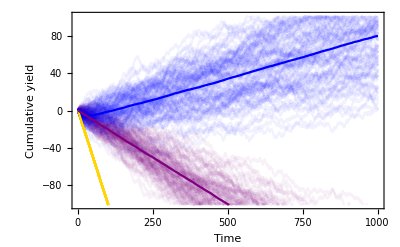

```mathematica
Show[stochcashpl,stochcoverpl,stochrandpl,mainpl,PlotRange->{All,{-101,101}},Joined->True,PlotStyle->{Blue,gold,Purple},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Time",14,Black],Style["Cumulative yield",14,Black]}]
```

```mathematica
Fit[randomisedzeoptsix⟦2⟧,x,x]
```

0.0743221 x

```mathematica
line=Fit[randomisedzeoptsix⟦2⟧, {1,x},x]
```

-10.3515+0.0898261 x

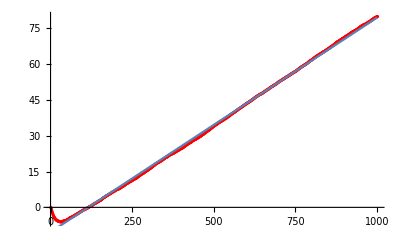

```mathematica
Show[ListPlot[randomisedzeoptsix⟦2⟧, PlotStyle->Red], Plot[line, {x, 0, 1000}]]
```

```mathematica
(line⟦2,1⟧+1)/2
```

0.544913